```mathematica
m=-2;f[x_]:=(1+x)^m;x0=0.2;
g[n_,x0_]:=D[f[x],{x,n}]/.x->x0;
s[n_,x_]:=Sum[g[k,x0]/(k!)*(x-x0)^k,{k,0,n}];
```

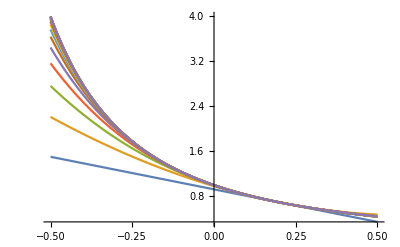

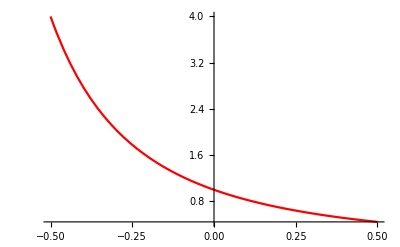

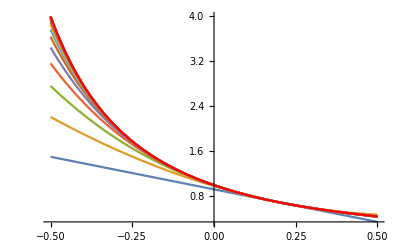

```mathematica
t=Table[s[n,x],{n,20}];
p1=Plot[Evaluate[t],{x,-1/2,1/2}];
p2=Plot[(1+x)^m,{x,-1/2,1/2},PlotStyle->RGBColor[1,0,0]];
Print[p1];
Print[p2];
Show[p1,p2,PlotRange->Full]
```